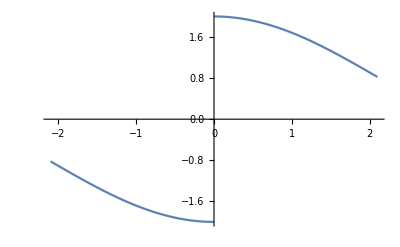

```mathematica
Plot[(√(2-2 Cos[2 x]))/x,{x,-2.1,2.1}]
```

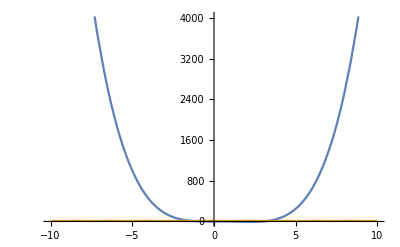

```mathematica
Plot[{x^4-3x^3,Cos[3x]+10},{x,-10,10}]
```

```mathematica
FindRoot[x^4-3x^3-Cos[3x]-10==0,{x,4}]
```

{x→3.2613}

```mathematica
FindRoot[x^4-3x^3-Cos[3x]-10==0,{x,-4}]
```

{x→-1.29206}

```mathematica
N[3.2613-1.29206]
```

1.96924

```mathematica
NSolve[x^6-29x^4-27x^2-90==0]
```

{{x→-5.47723},{x→-0.784873-1.05642 ⅈ},{x→-0.784873+1.05642 ⅈ},{x→0.784873-1.05642 ⅈ},{x→0.784873+1.05642 ⅈ},{x→5.47723}}

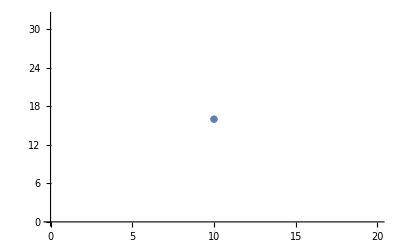

```mathematica
a=ListPlot[{{10,16}}]
```

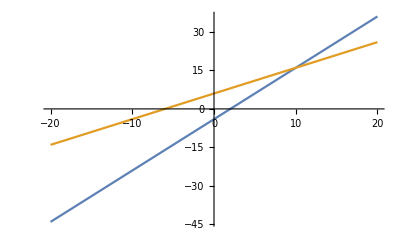

```mathematica
b=Plot[{2x-4,x+6},{x,-20,20}]
```

```mathematica
Show(a,b)
```

```mathematica
NSolve[x^5-8x^4-12x^3+236x^2-589x+372==0,x]
```

```mathematica
{{x->-5.5677643628300215},{x->1.},{x->2.999999999999997},{x->3.999999999999998 },{x->5.567764362830022}}
```

```mathematica
{{x->-2.5150072332186535},{x->-1.9010675717853696},{x->-1.1208164770063982} ,{x->6.768445641005211-3.5227305929669095 ⅈ},{x->6.768445641005211+3.5227305929669095 ⅈ}}
```

```mathematica
f[x_]:=(x+6)/(x-3)
g[x_]:=(2x-1)/(x-17)
f[g[x]]
```

```mathematica
Solve[(6+(-1+2 x)/(-17+x))/(-3+(-1+2 x)/(-17+x))==0,x]
```

{{x→103/8}}

```mathematica
(6+(-1+2 x)/(-17+x))/(-3+(-1+2 x)/(-17+x))
```

```mathematica
Solve[(15+(-1+2 x)/(-13+x))/(-3+(-1+2 x)/(-13+x))==0,x]
```

```mathematica
{{x->196/17}}

Clear[x]
```

```mathematica
f[x_]:=-4+0.1x^2
g[x_]:= ⅇ^-(0.01x^2)*Sin[2x]
```

```mathematica
Plot[{-4+0.1x^2,ⅇ^-(0.01x^2)*Sin[2x]},{x,-5,-5}]
```

Plot::plld: Endpoints for Charting`Private`pvar$32145 in {Charting`Private`pvar$32145,-5,-5} must have distinct machine-precision numerical values.

General::stop: Further output of Plot::plld will be suppressed during this calculation.

Plot[{-4+0.1 x^2,ⅇ^(-(0.01 x^2)) Sin[2 x]},{x,-5,-5}]

```mathematica
-
```